```mathematica
(*Import Steady state for κ=0.2,g=1.5*)
κ=0.2;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p2"];
Phi0p2=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p2[x_]:=Phi0p2[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p2[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

InterpolatingFunction::dmval: Input value {8.06134×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07038×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07944×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Finding eigenvalues and eigenfunctions*)
L=100;
dx=.05;
total=50;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
```

```mathematica
(*Calculating energy shift*)
λ4=4*Pi*Pi/3;
ωb=Sqrt[vals[[1]]];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}];
nshift=(3*κ*λ4/(4*ωb^2))*Vbbbb;
Equad[n_]:=n*ωb; (*free energy levels*)
Eshift[n_]:=n*ωb-n^2*nshift;(*energy levels with first order shift*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.584383}. NIntegrate obtained -0.0654836 and 1.79342×10^-7 for the integral and error estimates.

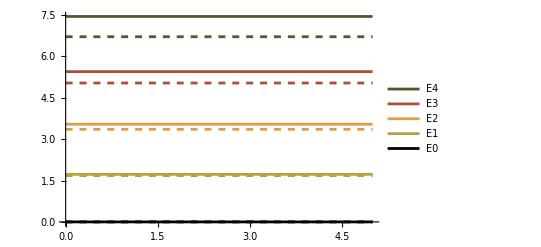

```mathematica
(*Energy levels plot, dotted lines are free and solid lines are shifted*)
Plot[{Eshift[4],Equad[4],Eshift[3],Equad[3],Eshift[2],Equad[2],Eshift[1],Equad[1],Eshift[0],Equad[0]},{x,0,5},PlotStyle->{ColorData["SandyTerrain"][1],{ColorData["SandyTerrain"][1],Dashed},ColorData["SandyTerrain"][0],{ColorData["SandyTerrain"][0],Dashed},ColorData["SandyTerrain"][.25],{ColorData["SandyTerrain"][.25],Dashed},ColorData["SandyTerrain"][.75],{ColorData["SandyTerrain"][.75],Dashed},Black,{Black,Dashed}},PlotLegends->{"E4",None,"E3",None,"E2",None,"E1",None,"E0",None}]
```

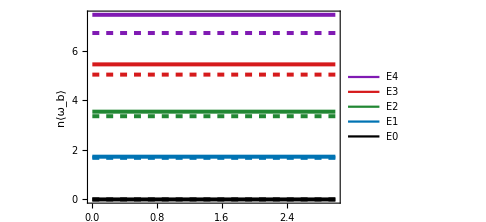

```mathematica
(*Pretty figure*)
c0=Black;
c1=RGBColor[0.00,0.45,0.70];
c2=RGBColor[0.13,0.53,0.20];
c3=RGBColor[0.84,0.10,0.11];
c4=RGBColor[0.50,0.10,0.70]; 

energyplot=Plot[{Eshift[4],Equad[4],Eshift[3],Equad[3],Eshift[2],Equad[2],Eshift[1],Equad[1],Eshift[0],Equad[0]},{x,0,3},PlotStyle->{{c4,Thickness[0.008]},{c4,Thickness[0.008],Dashed},{c3,Thickness[0.008]},{c3,Thickness[0.008],Dashed},{c2,Thickness[0.008]},{c2,Thickness[0.008],Dashed},{c1,Thickness[0.008]},{c1,Thickness[0.008],Dashed},{c0,Thickness[0.008]},{c0,Thickness[0.008],Dashed}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"},{5,"5"},{6,"6"},{7,"7"},{8,"8"}},None},{None,None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{None,Style["n⟨\!\(\*SubscriptBox[\(ω\), \(b\)]\)⟩",14]},PlotLegends->Placed[LineLegend[{c4,c3,c2,c1,c0},{Style["E4",12],Style["E3",12],Style["E2",12],Style["E1",12],Style["E0",12]},LegendLayout->"Column"],After],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{60,15},{15,15}},Background->White]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/energylevels_original.pdf",energyplot,ImageResolution->600]*)
```

-0.0654836

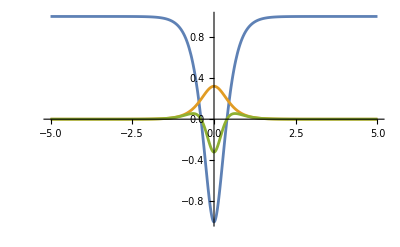

```mathematica
(*Storing data for energy levels at this κ*)
nvsEkappa0p2={{0,Eshift[0]},{1,Eshift[1]},{2,Eshift[2]},{3,Eshift[3]},{4,Eshift[4]}};
quadkappa0p2={{0,Equad[0]},{1,Equad[1]},{2,Equad[2]},{3,Equad[3]},{4,Equad[4]}};
(*Noting sign of shift at this κ*)
Vbbbb
(*Plot of overlap to understand sign*)
Plot[{cosTerm[x],fns[[1]]^4,cosTerm[x]*fns[[1]]^4},{x,-5,5}]
```

```mathematica
(*import steady state for κ=0.3,g=1.5*)
κ=0.3;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p3"];
Phi0p3=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p3[x_]:=Phi0p3[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p3[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

InterpolatingFunction::dmval: Input value {2.72665×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.7304×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.73415×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Eigensystem*)
L=100;
dx=.05;
total=50;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
```

```mathematica
(*Calculating energy shift*)
λ4=4*Pi*Pi/3;
ωb=Sqrt[vals[[1]]];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}];
nshift=(3*κ*λ4/(4*ωb^2))*Vbbbb;
Equad[n_]:=n*ωb;
Eshift[n_]:=n*ωb-n^2*nshift;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.193758}. NIntegrate obtained -0.127267 and 7.51162×10^-7 for the integral and error estimates.

-0.127267

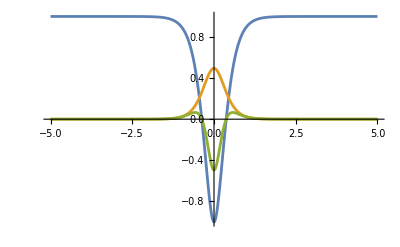

```mathematica
(*Storing energy shift at this κ*)
nvsEkappa0p3={{0,Eshift[0]},{1,Eshift[1]},{2,Eshift[2]},{3,Eshift[3]},{4,Eshift[4]}};
quadkappa0p3={{0,Equad[0]},{1,Equad[1]},{2,Equad[2]},{3,Equad[3]},{4,Equad[4]}};
(*Noting sign of shift at this κ*)
Vbbbb
(*Plot of overlap to understand sign*)
Plot[{cosTerm[x],fns[[1]]^4,cosTerm[x]*fns[[1]]^4},{x,-5,5}]
```

```mathematica
(*Import steady state for κ=0.1,g=1.5*)
κ=0.1;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p1"];
Phi0p1=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p1[x_]:=Phi0p1[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p1[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

InterpolatingFunction::dmval: Input value {1.08658×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.08745×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.08831×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
L=100;
dx=.05;
total=50;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
```

```mathematica
λ4=4*Pi*Pi/3;
ωb=Sqrt[vals[[1]]];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}];
nshift=(3*κ*λ4/(4*ωb^2))*Vbbbb;
Equad[n_]:=n*ωb;
Eshift[n_]:=n*ωb-n^2*nshift;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.782804}. NIntegrate obtained 0.00590027 and 1.61524×10^-8 for the integral and error estimates.

0.00590027

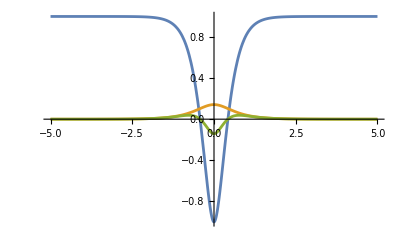

```mathematica
(*Storing energy shift at this κ*)
nvsEkappa0p1={{0,Eshift[0]},{1,Eshift[1]},{2,Eshift[2]},{3,Eshift[3]},{4,Eshift[4]}};
quadkappa0p1={{0,Equad[0]},{1,Equad[1]},{2,Equad[2]},{3,Equad[3]},{4,Equad[4]}};
(*Noting sign of shift at this κ*)
Vbbbb (*Note different sign here due to how delocalized the bound state is!*)
(*Plot of overlap to understand sign*)
Plot[{cosTerm[x],fns[[1]]^4,cosTerm[x]*fns[[1]]^4},{x,-5,5}]
```

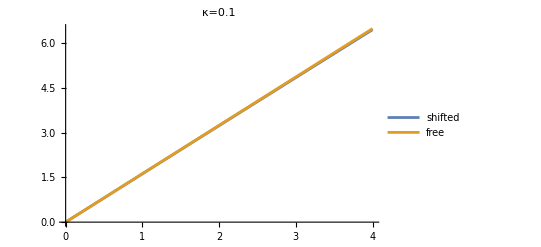

```mathematica
EvsNlist=ListLinePlot[{nvsEkappa0p1,quadkappa0p1},PlotLegends->{"shifted","free"},PlotLabel->"κ=0.1"]
```

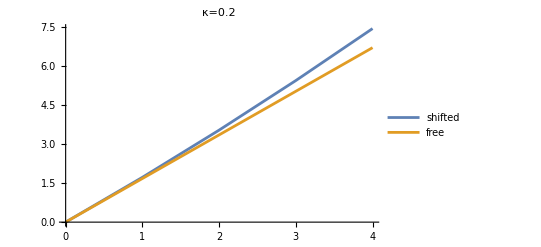

```mathematica
EvsNlist=ListLinePlot[{nvsEkappa0p2,quadkappa0p2},PlotLegends->{"shifted","free"},PlotLabel->"κ=0.2"]
```

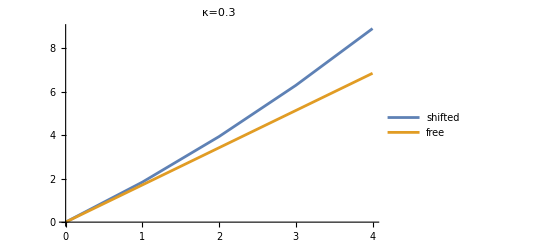

```mathematica
EvsNlist=ListLinePlot[{nvsEkappa0p3,quadkappa0p3},PlotLegends->{"shifted","free"},PlotLabel->"κ=0.3"]
```

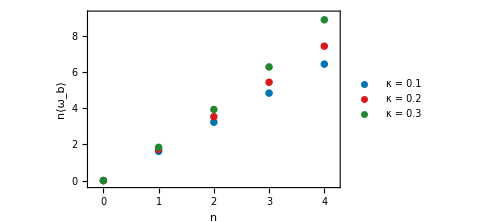

```mathematica
(*fancy plot of shifted frequencies with n*)
c1=RGBColor[0.00,0.45,0.70];
c2=RGBColor[0.84,0.10,0.11];
c3=RGBColor[0.13,0.53,0.20]; 

EvsNlist=ListPlot[{nvsEkappa0p1,nvsEkappa0p2,nvsEkappa0p3},PlotStyle->{{c1,PointSize[0.015]},{c2,PointSize[0.015]},{c3,PointSize[0.015]}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"},{5,"5"},{6,"6"},{7,"7"},{8,"8"},{9,"9"}},None},{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"}},None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["n",Italic,14],Style["n⟨\!\(\*SubscriptBox[\(ω\), \(b\)]\)⟩",14]},PlotLegends->Placed[LineLegend[{c1,c2,c3},{Style["κ = 0.1",12],Style["κ = 0.2",12],Style["κ = 0.3",12]},LegendLayout->"Column"],After],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White,PlotRange->{{-.2,4.2},{-.2,9.2}}]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/energydots_original.pdf",EvsNlist,ImageResolution->600]*)
```

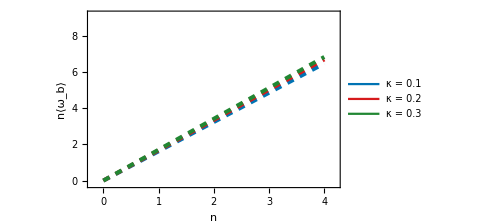

```mathematica
(*fancy plot of free energies with n*)
EvsNquad=ListLinePlot[{quadkappa0p1,quadkappa0p2,quadkappa0p3},PlotStyle->{{c1,Dashed,Thickness[0.008]},{c2,Dashed,Thickness[0.008]},{c3,Dashed,Thickness[0.008]}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"},{5,"5"},{6,"6"},{7,"7"},{8,"8"},{9,"9"}},None},{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"}},None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["n",Italic,14],Style["n⟨\!\(\*SubscriptBox[\(ω\), \(b\)]\)⟩",14]},PlotLegends->Placed[LineLegend[{c1,c2,c3},{Style["κ = 0.1",12],Style["κ = 0.2",12],Style["κ = 0.3",12]},LegendLayout->"Column"],After],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White,PlotRange->{{-.2,4.2},{-.2,9.2}}]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/energyquad_original.pdf",EvsNquad,ImageResolution->600]*)
```